## Simulation of the differential scanning calorimetry (DSC) curves of protein denaturation in the presence of varying amounts of a ligand Igor Sedov, igor_sedov@inbox.ru Citation: International Journal of Pharmaceutics, 583, 2020, 119362. https://doi.org/10.1016/j.ijpharm.2020.119362

Tested on Linux version of Mathematica 11

Simulation of DSC denaturation curves of bovine serum albumin in the presence of warfarin from our paper (Figures 1b, 4)

#### Input thermodynamic parameters of protein unfolding and ligand binding

```mathematica
unfoldingTemperature = 273.15 + 61.65(*Equilibrium temperature of protein unfolding in K, close but not exactly equal to the denaturation peak temperature for pure protein solution*); 
deltaHUnfolding = 612000(*Standard enthalpy of protein unfolding at unfoldingTemperature, J/mol*); 
deltaCpUnfolding =21000(*Standard heat capacity of protein unfolding, J/K/mol*); 
bindingK = 1.08*^5(*First binding constant of ligand to protein measured at referencebindingKTemperature*);
referencebindingKTemperature=298 ;
deltaHBinding = 18000(*Standard enthalpy of binding of the first ligand molecule to protein, J/mol*); 
bindingK2 = 2.28*^4(*Second binding constant of ligand to protein measured at referencebindingK2Temperature*); 
referencebindingK2Temperature=298 ;
deltaHBinding2 = deltaHBinding (*Standard enthalpy of binding of the second ligand molecule to protein, J/mol*); 
deltaSUnfolding = deltaHUnfolding/unfoldingTemperature(*Standard entropy of protein unfolding at unfoldingTemperature, J/K/mol*);
```

#### Input experimental details

```mathematica
proteinConcentration =7.2*^-5(*Concentration of protein solution, M*);
ligandConcentrations ={0.00001,0.25,0.5,0.75,1,1.25,1.5,1.75,2,3,4,5,6,7,8,9,10}*proteinConcentration (*Concentrations of ligand, M*);
cellVolume=0.3/1000(*DSC cell volume, L*);
startTemperature = 310(*Starting temperature of the DSC scan in K, must be below the denaturation peak onset for correct calculation of the enthalpy*);
endTemperature = 373(*End temperature of the DSC scan in K, must be above the denaturation peak endset for correct calculation of the enthalpy*);
temperatureStep = 0.1(*Temperature step of the simulated DSC curve in K, calculation time is inverse proportional to it, 0.1 K is usually sufficient*);
```

#### Run calculation

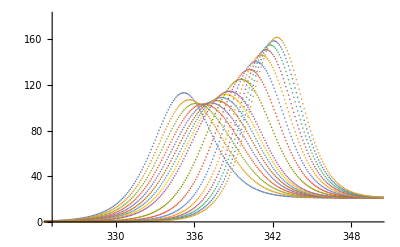

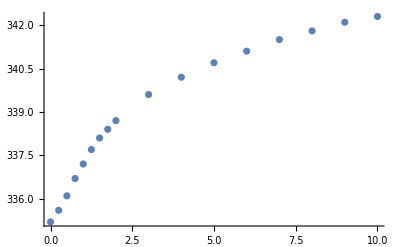

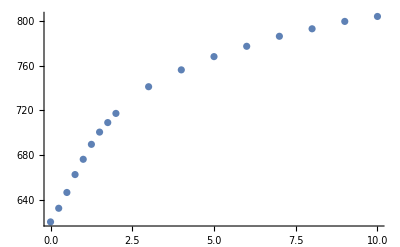

Peak temperatures, K
{335.2,335.6,336.1,336.7,337.2,337.7,338.1,338.4,338.7,339.6,340.2,340.7,341.1,341.5,341.8,342.1,342.3}
Observed denaturation enthalpies, kJ/mol
{620.4+0. ⅈ,632.57+0. ⅈ,646.668+0. ⅈ,662.655+0. ⅈ,676.29+0. ⅈ,689.637+0. ⅈ,700.567+0. ⅈ,709.07+0. ⅈ,717.252+0. ⅈ,741.085+0. ⅈ,756.121+0. ⅈ,767.952+0. ⅈ,777.166+0. ⅈ,786.109+0. ⅈ,792.794+0. ⅈ,799.381+0. ⅈ,803.803+0. ⅈ}

```mathematica
Clear[unfoldingKofT,bindingKofT,bindingK2ofT, equilibriumConcentrationsFunc];
unfoldingKofT=Exp[(deltaSUnfolding+deltaCpUnfolding*Log[#1/unfoldingTemperature]-(deltaHUnfolding+deltaCpUnfolding*(#1-unfoldingTemperature))/#1)/8.314]&;
bindingKofT=bindingK*Exp[-deltaHBinding/8.314*(1/referencebindingKTemperature-1/#1)]&;
bindingK2ofT=bindingK2*Exp[-deltaHBinding2/8.314*(1/referencebindingK2Temperature-1/#1)]&;
equilibriumConcentrationsFunc=Flatten[Table[Quiet[Solve[{denaturedConc+nativeConc+complexConc+complex2Conc==proteinConcentration,2*complex2Conc+complexConc+ligandConc==ligandTotalConc,complex2Conc/(complexConc*ligandConc)==bindingK2ofT[#1],complexConc/(nativeConc*ligandConc)==bindingKofT[#1],denaturedConc/nativeConc==unfoldingKofT[#1],denaturedConc>0,nativeConc>0,complexConc>0,complex2Conc>0,ligandConc>0},{denaturedConc,nativeConc,ligandConc,complexConc,complex2Conc}]],{ligandTotalConc,ligandConcentrations}],1]&;
temperatureList=Range[startTemperature,endTemperature,temperatureStep];
equilibriumConcentrations=Transpose[Values[Parallelize[Map[equilibriumConcentrationsFunc,temperatureList]]],{2,3,1}];
accumulatedHeat=cellVolume*(equilibriumConcentrations[[1]]*(deltaHUnfolding+deltaCpUnfolding*(temperatureList-unfoldingTemperature))-equilibriumConcentrations[[4]]*deltaHBinding-equilibriumConcentrations[[5]]*(deltaHBinding+deltaHBinding2));
differentialHeats=Differences[accumulatedHeat,{1,0}]/temperatureStep;
signalDSC=Transpose[Join[differentialHeats,{differentialHeats[[-1]]}]];
peakTemperatures=temperatureList[[Flatten[Ordering[#,-1]&/@signalDSC]]](*Peak maximum temperatures, K*);
approximatePeakAreas=deltaHUnfolding+deltaCpUnfolding*(peakTemperatures-unfoldingTemperature)+deltaHBinding*equilibriumConcentrations[[4,1]]/proteinConcentration+(deltaHBinding+deltaHBinding2)*equilibriumConcentrations[[5,1]]/proteinConcentration(*Observed enthalpies of protein denaturation obtained from the peak areas in J/mol, referenced to the peak maximum temperature, higher uncertainty for the double-humped peaks*);
plotSignal=Transpose[Join[{temperatureList},{#1}]]&/@(signalDSC/cellVolume/proteinConcentration/1000)(*Observed DSC signal (heat capacity) in kJ/K/mol*);
ListPlot[plotSignal,PlotRange->{{325,350},{0,180}}]
ListPlot[Transpose[{ligandConcentrations/proteinConcentration,peakTemperatures}]]
ListPlot[Transpose[{ligandConcentrations/proteinConcentration, approximatePeakAreas/1000}]]
Print["Peak temperatures, K\n",peakTemperatures,"\nObserved denaturation enthalpies, kJ/mol\n", approximatePeakAreas/1000]
```

Simulation of denaturation curves of RNAse A in the presence of 2’CMP at 200 mM KCI from Biochemistry, 1990, 29(29), 6927-40. doi: 10.1021/bi00481a024 (see Table 1)

#### Input thermodynamic parameters of protein unfolding and ligand binding

```mathematica
unfoldingTemperature = 273.15 + 61.24; 
deltaHUnfolding = 105000*4.184; 
deltaCpUnfolding = 1000*4.184; 
bindingK = 11500; 
referencebindingKTemperature=unfoldingTemperature ;
deltaHBinding = 17000*4.184; 
numberOfBindingSites = 1; 
deltaSUnfolding = deltaHUnfolding/unfoldingTemperature;
```

#### Input experimental details

```mathematica
proteinConcentration = 0.00014; 
ligandConcentrations = {0.0001,0.062,0.16,0.62,2.32,9.30,31}/1000;
cellVolume=0.5/1000; 
startTemperature = 310; 
endTemperature = 373; 
temperatureStep = 0.01;
```

#### Run calculation

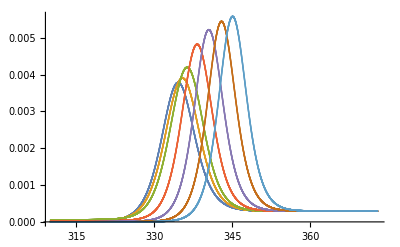

Peak temperatures, °C
{61.44,62.27,63.17,65.1,67.35,69.8,71.94}
Observed denaturation enthalpies, kcal/mol
{105.211,112.657,120.59,125.461,128.02,130.538,132.694}

```mathematica
Clear[unfoldingKofT,bindingKofT, equilibriumConcentrationsFunc];
unfoldingKofT=Exp[(deltaSUnfolding+deltaCpUnfolding*Log[#1/unfoldingTemperature]-(deltaHUnfolding+deltaCpUnfolding*(#1-unfoldingTemperature))/#1)/8.314]&;
bindingKofT=bindingK*Exp[-deltaHBinding/8.314*(1/referencebindingKTemperature-1/#1)]&;
equilibriumConcentrationsFunc=Flatten[Table[Quiet[Solve[{denaturedConc+nativeConc+complexConc==proteinConcentration,numberOfBindingSites*complexConc+ligandConc==ligandTotalConc,complexConc/(nativeConc*ligandConc^numberOfBindingSites)==bindingKofT[#1],denaturedConc/nativeConc==unfoldingKofT[#1],denaturedConc>0,nativeConc>0,complexConc>0,ligandConc>0},{denaturedConc,nativeConc,ligandConc,complexConc}]],{ligandTotalConc,ligandConcentrations}],1]&;
temperatureList=Range[startTemperature,endTemperature,temperatureStep];
equilibriumConcentrations=Transpose[Values[Parallelize[Map[equilibriumConcentrationsFunc,temperatureList]]],{2,3,1}];
accumulatedHeat=cellVolume*(equilibriumConcentrations[[1]]*(deltaHUnfolding+deltaCpUnfolding*(temperatureList-unfoldingTemperature))+equilibriumConcentrations[[3]]*deltaHBinding);
differentialHeats=Differences[accumulatedHeat,{1,0}]/temperatureStep;
signalDSC=Transpose[Join[differentialHeats,{differentialHeats[[-1]]}]];
peakTemperatures=temperatureList[[Flatten[Ordering[#,-1]&/@signalDSC]]];
approximatePeakAreas=deltaHUnfolding+deltaCpUnfolding*(peakTemperatures-unfoldingTemperature)+deltaHBinding*equilibriumConcentrations[[4,1]]/proteinConcentration;
plotSignal=Transpose[Join[{temperatureList},{#1}]]&/@signalDSC;
ListPlot[plotSignal,PlotRange->Full]
Print["Peak temperatures, °C\n",peakTemperatures-273.15,"\nObserved denaturation enthalpies, kcal/mol\n", approximatePeakAreas/4184]
```

The reproducibility of simulated denaturation curves of human serum albumin in the presence of 1,8-ANS from Anal. Biochem., 2006, 350, 277–284
 doi: 10.1016/j.ab.2005.12.029 (Figure 1)

#### Input thermodynamic parameters of protein unfolding and ligand binding

```mathematica
unfoldingTemperature = 273.15 + 60.1; 
deltaHUnfolding = 123000*4.184; 
deltaCpUnfolding = 6500*4.184; 
bindingK = 1.0*^6; 
referencebindingKTemperature=308.15 ;
deltaHBinding = 5000*4.184; 
bindingK2 = 2*8*^4; 
referencebindingK2Temperature=308.15 ;
deltaHBinding2 = 6000*4.184; 
bindingK3= 8*^4/2; 
referencebindingK3Temperature=308.15 ;
deltaHBinding3 = 6000*4.184; 
deltaSUnfolding = deltaHUnfolding/unfoldingTemperature;
```

#### Input experimental details

```mathematica
proteinConcentration = 0.00011; 
ligandConcentrations = {0.0001,0.4,0.8,1,1.5,2,3.5,5,10,20,50}*proteinConcentration ;
cellVolume=0.5/1000; 
startTemperature = 310; 
endTemperature = 373; 
temperatureStep = 0.1;
```

#### Run calculation

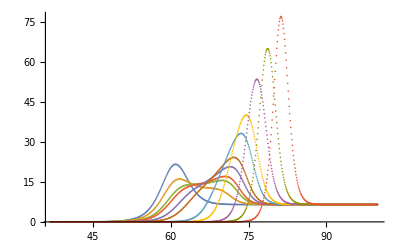

Peak temperatures, °C
{60.95,61.75,69.85,70.45,71.45,72.15,73.55,74.55,76.65,78.65,81.25}
Observed denaturation enthalpies, kcal/mol
{128.525+0. ⅈ,135.729+0. ⅈ,190.441+0. ⅈ,195.394+0. ⅈ,204.561+0. ⅈ,211.708+0. ⅈ,225.8+0. ⅈ,233.276+0. ⅈ,247.373+0. ⅈ,260.491+0. ⅈ,277.444+0. ⅈ}

```mathematica
Clear[unfoldingKofT,bindingKofT,bindingK2ofT, bindingK3ofT,equilibriumConcentrationsFunc];
unfoldingKofT=Exp[(deltaSUnfolding+deltaCpUnfolding*Log[#1/unfoldingTemperature]-(deltaHUnfolding+deltaCpUnfolding*(#1-unfoldingTemperature))/#1)/8.314]&;
bindingKofT=bindingK*Exp[-deltaHBinding/8.314*(1/referencebindingKTemperature-1/#1)]&;
bindingK2ofT=bindingK2*Exp[-deltaHBinding2/8.314*(1/referencebindingK2Temperature-1/#1)]&;
bindingK3ofT=bindingK3*Exp[-deltaHBinding3/8.314*(1/referencebindingK3Temperature-1/#1)]&;
equilibriumConcentrationsFunc=Flatten[Table[Quiet[Solve[{denaturedConc+nativeConc+complexConc+complex2Conc+complex3Conc==proteinConcentration,3*complex3Conc+2*complex2Conc+complexConc+ligandConc==ligandTotalConc,complex3Conc/(complex2Conc*ligandConc)==bindingK3ofT[#1],complex2Conc/(complexConc*ligandConc)==bindingK2ofT[#1],complexConc/(nativeConc*ligandConc)==bindingKofT[#1],denaturedConc/nativeConc==unfoldingKofT[#1],denaturedConc>0,nativeConc>0,complexConc>0,complex2Conc>0,complex3Conc>0,ligandConc>0},{denaturedConc,nativeConc,ligandConc,complexConc,complex2Conc,complex3Conc}]],{ligandTotalConc,ligandConcentrations}],1]&;
temperatureList=Range[startTemperature,endTemperature,temperatureStep];
equilibriumConcentrations=Transpose[Values[Parallelize[Map[equilibriumConcentrationsFunc,temperatureList]]],{2,3,1}];
accumulatedHeat=cellVolume*(equilibriumConcentrations[[1]]*(deltaHUnfolding+deltaCpUnfolding*(temperatureList-unfoldingTemperature))-equilibriumConcentrations[[4]]*deltaHBinding-equilibriumConcentrations[[5]]*(deltaHBinding+deltaHBinding2)-equilibriumConcentrations[[6]]*(deltaHBinding+deltaHBinding2+deltaHBinding3));
differentialHeats=Differences[accumulatedHeat,{1,0}]/temperatureStep;
signalDSC=Transpose[Join[differentialHeats,{differentialHeats[[-1]]}]];
peakTemperatures=temperatureList[[Flatten[Ordering[#,-1]&/@signalDSC]]];
approximatePeakAreas=deltaHUnfolding+deltaCpUnfolding*(peakTemperatures-unfoldingTemperature)+deltaHBinding*equilibriumConcentrations[[4,1]]/proteinConcentration+(deltaHBinding+deltaHBinding2)*equilibriumConcentrations[[5,1]]/proteinConcentration+(deltaHBinding+deltaHBinding2+deltaHBinding3)*equilibriumConcentrations[[6,1]]/proteinConcentration;
plotSignal=Transpose[Join[{temperatureList-273.15},{#1}]]&/@(signalDSC/cellVolume/proteinConcentration/4184);
ListPlot[plotSignal,PlotRange->Full]
Print["Peak temperatures, °C\n",peakTemperatures-273.15,"\nObserved denaturation enthalpies, kcal/mol\n", approximatePeakAreas/4184]
```